# Analytics

## Deriving the model dynamics

### Stationary population sizes of a wild - type only population

#### In old - habitat patches

In old-habitat patches, we assume that the wild-type local populations are at carrying capacity K_old

```mathematica
Nhatold=Subscript[K, old];
```

#### In new - habitat patches

The stationary population size is found recursively, by considering the different events in the life cycle, and assuming here that carrying capacity is not reached, so that there is no need for density regulation.

Note : for simplicity, we write f for f_old

```mathematica
Solve[x == (1-m+m(1-f)/(1-f+ ⅇ^πw f))Subscript[ωw, new] x+m (1-f)/(1-f+ⅇ^πw f)f/(1-f)Subscript[ωw, new] Subscript[K, old],x]//FullSimplify
solNhatnew=%⟦1⟧;
```

{{x→(f m K_old ωw_new)/(1+(-1+ⅇ^πw) f+(-1+f+ⅇ^πw f (-1+m)) ωw_new)}}

By definition, this population size cannot exceed K_new:

```mathematica
Nhatnew=Min[Subscript[K, new],x/.solNhatnew];
```

### Population sizes after dispersal, wild - type only population

#### In old - habitat patches

```mathematica
Ntildeold=(1-m +m (ⅇ^πw f)/(1-f + ⅇ^πw f))Nhatold+ m (ⅇ^πw f)/(1-f + ⅇ^πw f)(1-f)/f Nhatnew//FullSimplify
```

(-ⅇ^πw (-1+f) m Min[K_new,(f m K_old ωw_new)/(1+(-1+ⅇ^πw) f+(-1+f+ⅇ^πw f (-1+m)) ωw_new)]+(1-m+f (-1+ⅇ^πw+m)) K_old)/(1+(-1+ⅇ^πw) f)

#### In new - habitat patches

```mathematica
Ntildenew=(1-m + m (1-f)/(1-f + ⅇ^πw f))Nhatnew+m (1-f)/(1-f+ⅇ^πw f)f/(1-f)Nhatold//FullSimplify
```

(-(-1+f+ⅇ^πw f (-1+m)) Min[K_new,(f m K_old ωw_new)/(1+(-1+ⅇ^πw) f+(-1+f+ⅇ^πw f (-1+m)) ωw_new)]+f m K_old)/(1+(-1+ⅇ^πw) f)

### Per capita growth rate of mutants

#### In old - habitat patches

```mathematica
Subscript[a, old]=(Subscript[ωm, old] Subscript[K, old])/(Subscript[ωw, old] Ntildeold)-1;
```

#### In new - habitat patches

Since we assume that there is no density regulation in new - habitat patches because population size is below carrying capacity,

```mathematica
Subscript[a, new]=Subscript[ωm, new]-1;
```

## Establishment probability

### System to be numerically solved

```mathematica
Subscript[Eq, old]={1-Subscript[ϕ, old]== Exp[-(1-m (1-f)/(1-f + ⅇ^πm f))(1+Subscript[a, old])Subscript[ϕ, old]-m (1-f)/(1-f + ⅇ^πm f)(1+Subscript[a, new])Subscript[ϕ, new]]};
Subscript[Eq, new]={1-Subscript[ϕ, new]== Exp[-m (ⅇ^πm f)/(1-f + ⅇ^πm f)(1+Subscript[a, old])Subscript[ϕ, old]-(1-m (ⅇ^πm f)/(1-f + ⅇ^πm f))(1+Subscript[a, new])Subscript[ϕ, new]]};
```

```mathematica
syseq={Subscript[Eq, old],Subscript[Eq, new]};
```

### Approximation of the establishment probability

#### Definition of the Reproduction matrix

To avoid replacing a_oldand a_newby their expressions, we write them differently, as s_old and s_new
The matrix contain the expected number of successful offspring over the whole life cycle (including dispersal), i.e. the λ terms defined in the main text.

To avoid too lengthy expressions, we use μ_new and μ_old for the probabilites that a disperser goes to a new or old patch

```mathematica
reproMatrix={{(1-m Subscript[μ, new])(1+Subscript[s, old]),m Subscript[μ, new](1+Subscript[s, new])},{m Subscript[μ, old](1+Subscript[s, old]),(1-m Subscript[μ, old])(1+Subscript[s, new])}};
reproMatrix//MatrixForm
```

((1+s_old) (1-m μ_new) | m (1+s_new) μ_new
m (1+s_old) μ_old | (1+s_new) (1-m μ_old))

#### Largest eigenvalue of the reproduction matrix and Taylor - expansion

We search for the largest eigenvalue of this reproduction matrix
(the denominator is positive, so we pick the one with a + in front of the square root)

```mathematica
Eigenvalues[reproMatrix]
ρ=%⟦2⟧//FullSimplify;
```

{1/2 (2+s_new+s_old-m μ_new-m s_old μ_new-m μ_old-m s_new μ_old-√((-2-s_new-s_old+m μ_new+m s_old μ_new+m μ_old+m s_new μ_old)^2-4 (1+s_new+s_old+s_new s_old-m μ_new-m s_new μ_new-m s_old μ_new-m s_new s_old μ_new-m μ_old-m s_new μ_old-m s_old μ_old-m s_new s_old μ_old))),1/2 (2+s_new+s_old-m μ_new-m s_old μ_new-m μ_old-m s_new μ_old+√((-2-s_new-s_old+m μ_new+m s_old μ_new+m μ_old+m s_new μ_old)^2-4 (1+s_new+s_old+s_new s_old-m μ_new-m s_new μ_new-m s_old μ_new-m s_new s_old μ_new-m μ_old-m s_new μ_old-m s_old μ_old-m s_new s_old μ_old)))}

Define assumptions on the parameters to help Mathematical simplify solutions
(note that both ϵ>0 or ϵ<0 work. But one needs to assume one for Mathematica to solve the square roots)

```mathematica
assumptions={m>0&&m<1&&Subscript[π, m]∈Reals&&Subscript[π, w]∈Reals&&ϵ>0&&Subscript[s, new]>0&&ξ>0&&f>0&&f<1&&Subscript[s, new]>Subscript[s, old]};
```

Define scaling to rescale parameters as function of ϵ, assumed to be small

```mathematica
scaling={m->ϵ mm,Subscript[s, old]->ϵ Subscript[ss, old],Subscript[s, new]->ϵ Subscript[ss, new]};
```

Taylor - expand the eigenvalue, at the first order in ϵ (after rescaling), and simplify

```mathematica
Assuming[assumptions,Series[ρ/.scaling,{ϵ,0,1}]//Normal//FullSimplify]
```

1+1/2 ϵ (ss_new+ss_old-mm (μ_new+μ_old)+√((ss_new-ss_old+mm μ_new)^2+2 mm (-ss_new+ss_old+mm μ_new) μ_old+mm^2 μ_old^2))

#### Eigenvectors

Left eigenvector associated to the largest eigenvalue (second one in the order of vectors in the output)

```mathematica
u=Eigenvectors[Transpose[reproMatrix]]⟦2⟧//FullSimplify;
```

Right eigenvector

```mathematica
v=Eigenvectors[reproMatrix]⟦2⟧//FullSimplify;
```

Normalize the eigenvectors 
Find the coefficients satisfying the following constraints (lev = left eigenvector, rev  = right eigenvector, the numbers refer to the elements)

```mathematica
Solve[{a (lev1+lev2)==1,a lev1 b rev1+a lev2 b rev2==1},{a,b}]
```

{{a→1/(lev1+lev2),b→(lev1+lev2)/(lev1 rev1+lev2 rev2)}}

a is the sum of the elements of the left eigenvector, b' s denominator is the product of the vectors. The normalized vectors (n) are therefore

```mathematica
un=1/Total[u] u;
vn=Total[u]/(u.v)v;
```

#### Approximate establishment probability

Directly applying Theorem 5.6 from Haccou et al.(2005)

We define

```mathematica
B=∑_(i=1)^2 (un⟦i⟧(∑_(j=1)^2 vn⟦j⟧reproMatrix⟦i,j⟧))+ρ(1-ρ)(∑_(j=1)^2 un⟦j⟧vn⟦j⟧^2);
```

and according to the theorem, the approximate establishment probabilities are then

```mathematica
exactϕ=(2(ρ-1)vn)/B;
```

which we Taylor - Expand as (this takes a few seconds/minutes)

```mathematica
solutions = Assuming[assumptions,Assuming[assumptions, Normal[Series[exactϕ/.scaling,{ϵ,0,1}]]]];
```

and we recover the original parameters (this also takes a few seconds/minutes)

```mathematica
backscaling = {mm-> m/ϵ,Subscript[ss, old]-> Subscript[s, old]/ϵ,Subscript[ss, new]-> Subscript[s, new]/ϵ};
backsolutions=Assuming[assumptions,FullSimplify[solutions/.backscaling]]
```

{(-s_new (s_old-2 m μ_new)+s_old (s_old-m μ_new+m μ_old+√((s_new-s_old+m μ_new)^2+2 m (-s_new+s_old+m μ_new) μ_old+m^2 μ_old^2)))/(√((s_new-s_old+m μ_new)^2+2 m (-s_new+s_old+m μ_new) μ_old+m^2 μ_old^2)),(s_new^2+2 m s_old μ_old+s_new (-s_old+m μ_new-m μ_old+√((s_new-s_old+m μ_new)^2+2 m (-s_new+s_old+m μ_new) μ_old+m^2 μ_old^2)))/(√((s_new-s_old+m μ_new)^2+2 m (-s_new+s_old+m μ_new) μ_old+m^2 μ_old^2))}

Extract the two establishment probabilities, and recover the model parameters

```mathematica
recoverparams={Subscript[μ, new]-> (1-f)/(1-f + ⅇ^πm f),Subscript[μ, old]-> (ⅇ^πm f)/(1-f + ⅇ^πm f),Subscript[s, old]->Subscript[a, old],Subscript[s, new]->Subscript[a, new]};
```

```mathematica
Subscript[ϕapprox, old]=backsolutions⟦1⟧/.recoverparams;
Subscript[ϕapprox, new]=backsolutions⟦2⟧/.recoverparams;
```

# Figures

## Initializations

### Parameters

```mathematica
constantParam={Subscript[K, old]->1000,Subscript[K, new]->500,Subscript[ωw, old]->1.5,Subscript[ωw, new]->0.75,Subscript[ωm, new]->1.02};
```

The other default parameters are
f = 0.5, 
m = 0.06,
ωm_old=1.45 or 1.35

```mathematica
mdefault=0.06;
fdefault=0.5;
Subscript[ωmdefault1, old]=1.35;
Subscript[ωmdefault2, old]=1.45;
```

```mathematica
π0={πw->0,πm->0};
πOO={πw->1/2,πm->1/2};
πON={πw->1/2,πm-> -1/2};
πNO={πw->-1/2,πm-> 1/2};
πNN={πw->-1/2,πm-> -1/2};
```

Emigration probability m

```mathematica
mmin=10^-3; (* minimum value *)
mmax=1; (* max value *)
nm=101; (* number of values *)
logmvals=Table[Log10[mmin]+((Log10[mmax]-Log10[mmin])(i-1))/(nm-1),{i,1,nm}];
mvals=Table[10^logmvals⟦i⟧,{i,1,nm}];
```

### Plotting parameters

```mathematica
col0 =Black;
colOO=Blue;
colON=Orange;
colNO=Red;
colNN=Green;
```

```mathematica
mark0=●;
markOO=▲;
markON=■;
markNO=◆;
markNN=▼;
```

## Population variables

### Nhatold and Nhatnew, the population densities of the wild-type population at the beginning of a generation

#### Only for unbiaised dispersal

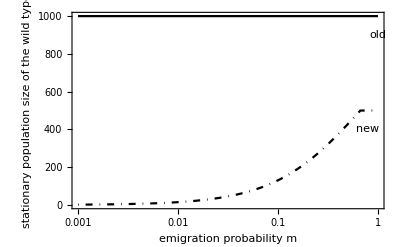

```mathematica
Show[LogLinearPlot[{Nhatold/.constantParam,Nhatnew/.constantParam/.{f->fdefault}/.π0},{m,mmin,mmax},PlotStyle->{{col0,Full},{col0,DotDashed}},AxesOrigin->{mmin,0},Frame->{True,True,False,False}, FrameLabel->{"emigration probability m", "stationary population size of the wild type"}],Graphics[Text["old",{0,900}]],Graphics[Text["new",{-0.25,400}]]]
```

#### For all WT dispersal biases

(The dispersal bias of the mutant does not affect the population size of the wild - type population)

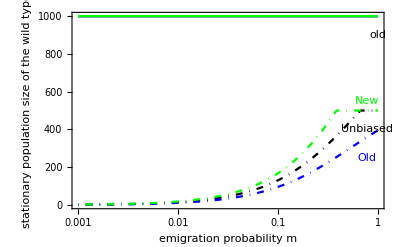

```mathematica
Show[LogLinearPlot[{Nhatold/.constantParam,Nhatnew/.constantParam/.{f->fdefault}/.π0},{m,mmin,mmax},PlotStyle->{{col0,Full},{col0,DotDashed}},AxesOrigin->{mmin,0},Frame->{True,True,False,False}, FrameLabel->{"emigration probability m", "stationary population size of the wild type"}],
LogLinearPlot[{Nhatold/.constantParam,Nhatnew/.constantParam/.{f->fdefault}/.πOO},{m,mmin,mmax},PlotStyle->{{colOO,Full},{colOO,DotDashed}}],
LogLinearPlot[{Nhatold/.constantParam,Nhatnew/.constantParam/.{f->fdefault}/.πNN},{m,mmin,mmax},PlotStyle->{{colNN,Full},{colNN,DotDashed}}],Graphics[Text["old",{0,900}]],Graphics[Text[Style["Old", colOO],{-0.25,250}]],
Graphics[Text[Style["New", colNN],{-0.25,550}]],
Graphics[Text[Style["Unbiased",Small],{-0.25,400}]]]
```

With other values of f_old

```mathematica
Do[Subscript[P, thef]=Show[LogLinearPlot[{Nhatold/.constantParam,Nhatnew/.constantParam/.{f->thef}/.π0},{m,mmin,mmax},PlotStyle->{{col0,Full},{col0,DotDashed}},AxesOrigin->{mmin,0},Frame->{True,True,False,False}, FrameLabel->{"emigration probability m", "stationary population size of the wild type"}],
LogLinearPlot[{Nhatold/.constantParam,Nhatnew/.constantParam/.{f->thef}/.πOO},{m,mmin,mmax},PlotStyle->{{colOO,Full},{colOO,DotDashed}}],
LogLinearPlot[{Nhatold/.constantParam,Nhatnew/.constantParam/.{f->thef}/.πNN},{m,mmin,mmax},PlotStyle->{{colNN,Full},{colNN,DotDashed}}],Graphics[Text["old",{0,900}]],Graphics[Text[Style["Old", colOO],{-0.25,250}]],
Graphics[Text[Style["New", colNN],{-0.25,550}]],
Graphics[Text[Style["Unbiased",Small],{-0.25,400}]],PlotLabel->"f_old="<>ToString[thef]]
,{thef,{0.25,0.75}}]
```

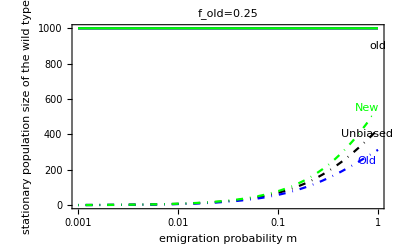

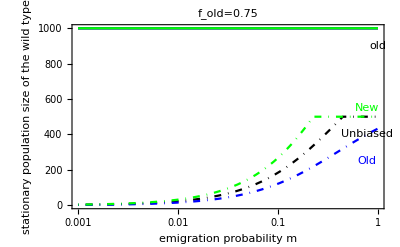

```mathematica
Subscript[P, 0.25]
Subscript[P, 0.75]
```

### Ntildeold and Ntildenew, the population densities of the wild - type population right after dispersal

#### Only for unbiaised dispersal

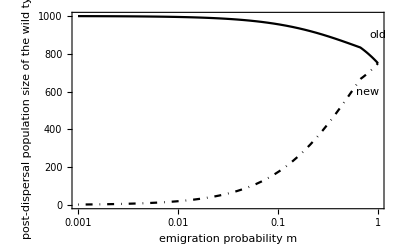

```mathematica
Show[LogLinearPlot[{Ntildeold/.constantParam/.{f->fdefault}/.π0,Ntildenew/.constantParam/.{f->fdefault}/.π0},{m,mmin,mmax},PlotStyle->{{col0,Full},{col0,DotDashed}},AxesOrigin->{mmin,0},Frame->{True,True,False,False}, FrameLabel->{"emigration probability m", "post-dispersal population size of the wild type"}],Graphics[Text["old",{0,900}]],Graphics[Text["new",{-0.25,600}]]]
```

#### For all WT dispersal biases

Again, dispersal bias of the mutant has no influence

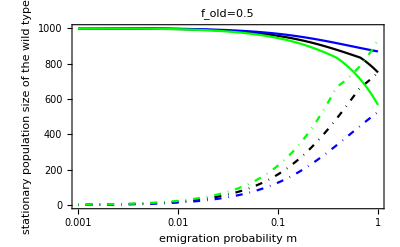

```mathematica
Show[LogLinearPlot[{Ntildeold/.constantParam/.{f->fdefault}/.π0,Ntildenew/.constantParam/.{f->fdefault}/.π0},{m,mmin,mmax},PlotStyle->{{col0,Full},{col0,DotDashed}},AxesOrigin->{mmin,0},Frame->{True,True,False,False}, FrameLabel->{"emigration probability m", "stationary population size of the wild type"}],
LogLinearPlot[{Ntildeold/.constantParam/.{f->fdefault}/.πOO,Ntildenew/.constantParam/.{f->fdefault}/.πOO},{m,mmin,mmax},PlotStyle->{{colOO,Full},{colOO,DotDashed}}],
LogLinearPlot[{Ntildeold/.constantParam/.{f->fdefault}/.πNN,Ntildenew/.constantParam/.{f->fdefault}/.πNN},{m,mmin,mmax},PlotStyle->{{colNN,Full},{colNN,DotDashed}}],PlotLabel->"f_old="<>ToString[fdefault]]
```

For other values of f_old

```mathematica
Do[Subscript[P, thef]=
Show[LogLinearPlot[{Ntildeold/.constantParam/.{f->thef}/.π0,Ntildenew/.constantParam/.{f->thef}/.π0},{m,mmin,mmax},PlotStyle->{{col0,Full},{col0,DotDashed}},AxesOrigin->{mmin,0},Frame->{True,True,False,False}, FrameLabel->{"emigration probability m", "stationary population size of the wild type"}],
LogLinearPlot[{Ntildeold/.constantParam/.{f->thef}/.πOO,Ntildenew/.constantParam/.{f->thef}/.πOO},{m,mmin,mmax},PlotStyle->{{colOO,Full},{colOO,DotDashed}}],
LogLinearPlot[{Ntildeold/.constantParam/.{f->thef}/.πNN,Ntildenew/.constantParam/.{f->thef}/.πNN},{m,mmin,mmax},PlotStyle->{{colNN,Full},{colNN,DotDashed}}],PlotLabel->"f_old="<>ToString[thef]],{thef,{0.25,0.75}}]
```

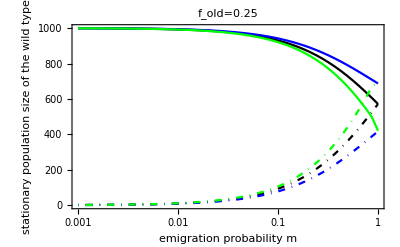

```mathematica
Subscript[P, 0.25]
```

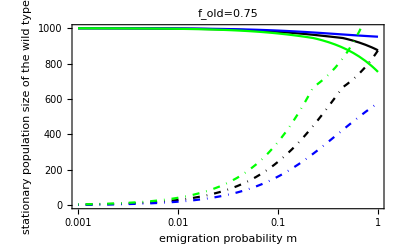

```mathematica
Subscript[P, 0.75]
```

#### a_old, the per capita local growth rate of the mutant

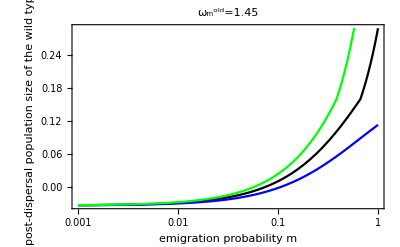

```mathematica
Show[LogLinearPlot[Subscript[a, old]/.constantParam/.{f->fdefault,Subscript[ωm, old]->Subscript[ωmdefault2, old]}/.π0,{m,mmin,mmax},PlotStyle->{{col0,Full},{col0,DotDashed}},AxesOrigin->{mmin,0},Frame->{True,True,False,False}, FrameLabel->{"emigration probability m", "post-dispersal population size of the wild type"}],
LogLinearPlot[Subscript[a, old]/.constantParam/.{f->fdefault,Subscript[ωm, old]->Subscript[ωmdefault2, old]}/.πOO,{m,mmin,mmax},PlotStyle->{{colOO,Full},{colOO,DotDashed}}],
LogLinearPlot[Subscript[a, old]/.constantParam/.{f->fdefault,Subscript[ωm, old]->Subscript[ωmdefault2, old]}/.πNN,{m,mmin,mmax},PlotStyle->{{colNN,Full},{colNN,DotDashed}}],Graphics[Text["old",{0,900}]],Graphics[Text["new",{-0.25,600}]],
PlotLabel->"ω_m^old="<>ToString[Subscript[ωmdefault2, old]]]
```

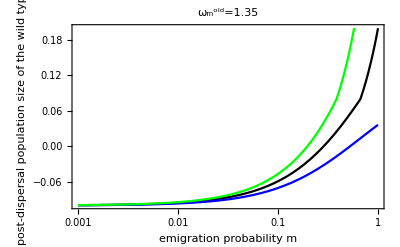

```mathematica
Show[LogLinearPlot[Subscript[a, old]/.constantParam/.{f->fdefault,Subscript[ωm, old]->Subscript[ωmdefault1, old]}/.π0,{m,mmin,mmax},PlotStyle->{{col0,Full},{col0,DotDashed}},AxesOrigin->{mmin,0},Frame->{True,True,False,False}, FrameLabel->{"emigration probability m", "post-dispersal population size of the wild type"}],
LogLinearPlot[Subscript[a, old]/.constantParam/.{f->fdefault,Subscript[ωm, old]->Subscript[ωmdefault1, old]}/.πOO,{m,mmin,mmax},PlotStyle->{{colOO,Full},{colOO,DotDashed}}],
LogLinearPlot[Subscript[a, old]/.constantParam/.{f->fdefault,Subscript[ωm, old]->Subscript[ωmdefault1, old]}/.πNN,{m,mmin,mmax},PlotStyle->{{colNN,Full},{colNN,DotDashed}}],Graphics[Text["old",{0,900}]],Graphics[Text["new",{-0.25,600}]],
PlotLabel->"ω_m^old="<>ToString[Subscript[ωmdefault1, old]]]
```

# Tests -- Sandbox

### Test new anew

```mathematica
Subscript[a2, new]=If[Nhatnew<Subscript[K, new],Subscript[ωm, new]-1,(Subscript[ωm, new] Subscript[K, new])/(Subscript[ωw, new] ((1-m + m (1-f)/(1-f + ⅇ^πw f))Subscript[K, new]+m (1-f)/(1-f+ⅇ^πw f)f/(1-f)Subscript[K, old]))-1];
```

```mathematica
Subscript[Eq2, old]={1-Subscript[ϕ, old]== Exp[-(1-m (1-f)/(1-f + ⅇ^πm f))(1+Subscript[a, old])Subscript[ϕ, old]-m (1-f)/(1-f + ⅇ^πm f)(1+Subscript[a2, new])Subscript[ϕ, new]]};
Subscript[Eq2, new]={1-Subscript[ϕ, new]== Exp[-m (ⅇ^πm f)/(1-f + ⅇ^πm f)(1+Subscript[a, old])Subscript[ϕ, old]-(1-m (ⅇ^πm f)/(1-f + ⅇ^πm f))(1+Subscript[a2, new])Subscript[ϕ, new]]};
syseq2={Subscript[Eq2, old],Subscript[Eq2, new]};
```

Numerically solving the establishment probabilities

```mathematica
FindRoot[Evaluate[{Subscript[Eq, old],Subscript[Eq, new]}/.constantParam/.{f->fdefault,m->mdefault,Subscript[ωm, old]->Subscript[ωmdefault1, old]}/.π0],{{Subscript[ϕ, old],0.5},{Subscript[ϕ, new],0.5}}]
```

{ϕ_old→-5.17288×10^-16,ϕ_new→-1.26875×10^-15}

Plotting simulation data

```mathematica
SetDirectory["/Users/flo/Documents/Work/Projects/1_EnCours/2018_RescuePete/code"]
```

/Users/flo/Documents/Work/Projects/1_EnCours/2018_RescuePete/code

```mathematica
aa=Import["../evolutionary_rescue_and_dispersal/Fig2/c/vary_mu_phi1_pi1_m05_pi2_m05.csv"]
```

{{0.00063,0.001},{0.17221,1},{0.00097,0.0015},{0.00158,0.002},{0.00252,0.004},{0.00311,0.005},{0.0018,0.003},{0.00431,0.008},{0.004,0.006},{0.01236,0.03},{0.01905,0.05},{0.00582,0.01},{0.00747,0.015},{0.00978,0.02},{0.09143,0.2},{0.12979,0.3},{0.1488,0.8},{0.06739,0.15},{0.01566,0.04},{0.14745,0.4},{0.02323,0.06},{0.13768,0.6},{0.04182,0.1},{0.03361,0.08},{0.14112,0.5}}

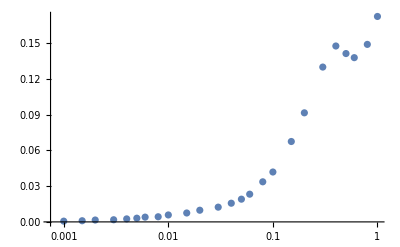

```mathematica
ListLogLinearPlot[Table[{aa[[i,2]],aa[[i,1]]},{i,1,Length[aa]}]]
```

Emigration probability m

```mathematica
mmin=10^-4; (* minimum value *)
mmax=1; (* max value *)
nm=201; (* number of values *)
logmvals=Table[Log10[mmin]+((Log10[mmax]-Log10[mmin])(i-1))/(nm-1),{i,1,nm}];
mvals=Table[10^logmvals⟦i⟧,{i,1,nm}];
```

```mathematica
PhiOnn=Table[0,{i,1,nm}];
PhiNnn=PhiOnn;
PhiNnn2=PhiOnn2=PhiOnn;
```

```mathematica
Do[
sols1=FindRoot[Evaluate[syseq/.constantParam/.{f->fdefault,m->mvals⟦i⟧,Subscript[ωm, old]->Subscript[ωmdefault2, old]}/.πNN],{{Subscript[ϕ, old],0.5},{Subscript[ϕ, new],0.5}}];
PhiOnn⟦i⟧=Subscript[ϕ, old]/.sols1;
PhiNnn⟦i⟧=Subscript[ϕ, new]/.sols1;

sols2=FindRoot[Evaluate[syseq2/.constantParam/.{f->fdefault,m->mvals⟦i⟧,Subscript[ωm, old]->Subscript[ωmdefault2, old]}/.πNN],{{Subscript[ϕ, old],0.5},{Subscript[ϕ, new],0.5}}];
PhiOnn2⟦i⟧=Subscript[ϕ, old]/.sols2;
PhiNnn2⟦i⟧=Subscript[ϕ, new]/.sols2;
,{i,1,nm}]
```

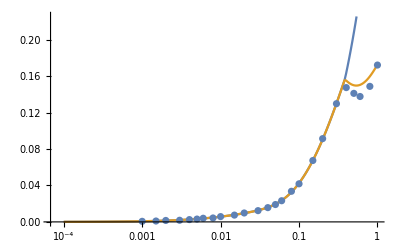

```mathematica
Show[ListLogLinearPlot[{Table[{mvals⟦i⟧,PhiOnn⟦i⟧},{i,1,nm}],Table[{mvals⟦i⟧,PhiOnn2⟦i⟧},{i,1,nm}]},Joined->True],ListLogLinearPlot[Table[{aa[[i,2]],aa[[i,1]]},{i,1,Length[aa]}]]]
```